# Thomson Problem

```mathematica
n=6;
dgt=10;
δ=N[10^-1,dgt];
κ=N[4*10^-1,dgt];
```

### Initial condition

```mathematica
(*Here the initial positions are generated randomly*)
Do[θ0[i]=RandomReal[{0,Pi},WorkingPrecision->dgt];
ϕ0[i]=RandomReal[{0,2 Pi},WorkingPrecision->dgt];
r0[i]={Sin[θ0[i]] Cos[ϕ0[i]],Sin[θ0[i]] Sin[ϕ0[i]],Cos[θ0[i]]};,{i,1,n}]
(*Here the initial velocities are generated randomly*)
Do[vθ0[i]=RandomReal[{0,1},WorkingPrecision->dgt];
vϕ0[i]=RandomReal[{0,1},WorkingPrecision->dgt];,{i,1,n}]
initialpositions=Table[r0[i],{i,1,n}];
(*Plot for the initial state*)
m1=ListPointPlot3D[initialpositions,PlotStyle->PointSize[0.02],PlotRange->{{-1,1},{-1,1},{-1,1}}];
m2=Graphics3D[{Black,Opacity[.1],Sphere[{0,0,0}]},Axes->True,PlotRange->1];
m3=Show[m2,m1]
```

-Graphics3D-

### Euler-Lagrange Equations

```mathematica
(*Euler-Lagrange Equation for θ*)
table1=Table[{Subscript[θ, i]''[t]-(Subscript[ϕ, i]'[t])^2*Sin[Subscript[θ, i][t]]*Cos[Subscript[θ, i][t]]+Sum[If[i≠j,1/(4 √2) *((Cos[Subscript[θ, i][t]]*Sin[Subscript[θ, j][t]]*Cos[Subscript[ϕ, i][t]-Subscript[ϕ, j][t]]-Sin[Subscript[θ, i][t]]*Cos[Subscript[θ, j][t]])/((1-Cos[Subscript[θ, i][t]]*Cos[Subscript[θ, j][t]]-Sin[Subscript[θ, i][t]]*Sin[Subscript[θ, j][t]]*Cos[Subscript[ϕ, i][t]-Subscript[ϕ, j][t]]+δ)^(3/2))),0],{j,1,n}]+κ*Subscript[θ, i]'[t]==0,Subscript[θ, i][0]==θ0[i],Subscript[θ, i]'[0]==vθ0[i]},{i,1,n}];
(*Euler-Lagrange Equation for ϕ*)
table2=Table[{Subscript[ϕ, i]''[t]*(Sin[Subscript[θ, i][t]])^2+2*Subscript[ϕ, i]'[t]*Subscript[θ, i]'[t]*Cos[Subscript[θ, i][t]]*Sin[Subscript[θ, i][t]]-Sum[If[i≠j,1/(4 √2) *((Sin[Subscript[θ, i][t]]*Sin[Subscript[θ, j][t]]*Sin[Subscript[ϕ, i][t]-Subscript[ϕ, j][t]])/((1-Cos[Subscript[θ, i][t]]*Cos[Subscript[θ, j][t]]-Sin[Subscript[θ, i][t]]*Sin[Subscript[θ, j][t]]*Cos[Subscript[ϕ, i][t]-Subscript[ϕ, j][t]]+δ)^(3/2))),0],{j,1,n}]+κ*Subscript[ϕ, i]'[t]==0,Subscript[ϕ, i][0]==ϕ0[i],Subscript[ϕ, i]'[0]==vϕ0[i]},{i,1,n}];
(*Vector for the variables*)
vars1=Table[{Subscript[θ, i][t],Subscript[ϕ, i][t]},{i,1,n}];
vars=Flatten[Partition[Flatten[vars1],1]];
```

### Solutions

```mathematica
g=NDSolve[{table1,table2},vars,{t,0,400},WorkingPrecision->dgt][[1]];
y[t_]:=Evaluate[vars/.g]
result=Table[{Sin[y[t][[2*k-1]]] Cos[y[t][[2*k]]],Sin[y[t][[2*k-1]]] Sin[y[t][[2*k]]],Cos[y[t][[2*k-1]]]},{k,1,n}];
trayectories=ParametricPlot3D[result,{t,0,400},PlotRange->{{-1,1},{-1,1},{-1,1}}];
Show[trayectories,m2]
```

-Graphics3D-

### Final Positions

```mathematica
final=400;
finalpositions=N[Table[{Sin[y[final][[2*k-1]]] Cos[y[final][[2*k]]],Sin[y[final][[2*k-1]]] Sin[y[final][[2*k]]],Cos[y[final][[2*k-1]]]},{k,1,n}],dgt];
m3=ListPointPlot3D[finalpositions,PlotRange->{{-1,1},{-1,1},{-1,1}},PlotStyle->PointSize[0.02]];
Show[m2,m3]
```

-Graphics3D-

### Coulomb Dimensionless Energy

```mathematica
Sum[If[i≠j,1/2 1/Sqrt[FullSimplify[Expand[(finalpositions[[i]]-finalpositions[[j]]).(finalpositions[[i]]-finalpositions[[j]])]]],0],{i,1,n},{j,1,n}]
```

9.98528138

### Polyhedron

```mathematica
Graphics3D[{EdgeForm[Red],Red,Specularity[White,5],Polygon[Part[finalpositions,#]&/@Subsets[Range[Length@finalpositions],{3}]]},Boxed->True,Axes->True]
```

-Graphics3D-

### Dipole Moment

```mathematica
dipolemoment=Sum[N[finalpositions[[i]]],{i,1,n}] ;
Norm[dipolemoment]
```

0.0000394104

### Interpolating functions

```mathematica
datapaper={{2,0.50000000},{3,1.73205081},{4,3.67423461},{5,6.47469149},{6,9.98528137},{7,14.45297741},{8,19.67528786},{9,25.75998653},{10,32.71694946},{11,40.59645051},{12,49.16525306},{13,58.85323061},{14,69.30636330},{15,80.67024411},{16,92.91165530},{17,106.05040483},{18,120.08446745},{19,135.08946756},{20,150.88156833},{21,167.64162240},{22,185.28753615},{23,203.93019066},{24,223.34707405},{25,243.81276030},{26,265.13332632},{27,287.30261503},{28,310.49154236},{29,334.63443992},{30,359.60394590},{31,385.53083806},{32,412.26127465},{33,440.20405745},{34,468.90485328}};
dataprogram={{2,0.500000000},{3,1.7320508076},{4,3.67423461},{5,6.474691495},{6,9.98528137},{7,14.452977431},{8,19.67539562},{9,25.75999330},{10,32.7169774},{11,40.59670773},{12,49.1652531},{13,58.85329068},{14,69.3068842},{15,80.67071383},{16,92.9123854},{17,106.05071369},{18,120.0848708},{19,135.09079279},{20,150.882827316},{21,167.6419753},{22,185.2885181},{23,203.9320202},{24,223.3487659},{25,243.8143661},{26,265.1354032},{27,287.3033539},{28,310.4928308},{29,334.6381400},{30,359.6070077},{31,385.5330279},{32,412.2612747},{33,440.2062345},{34,468.9091069}};
```

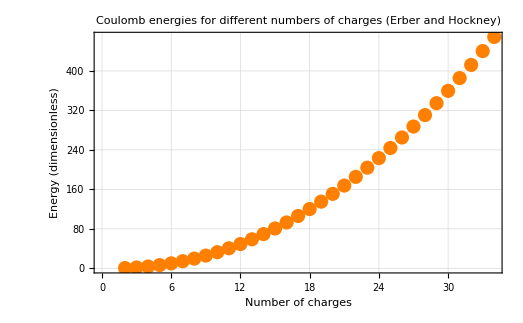

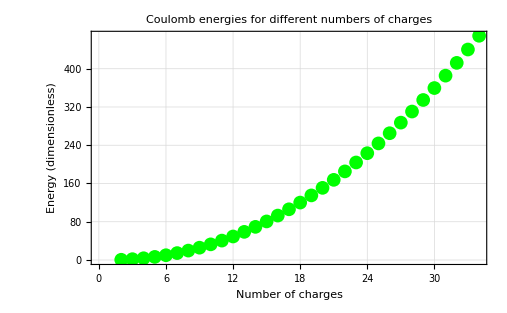

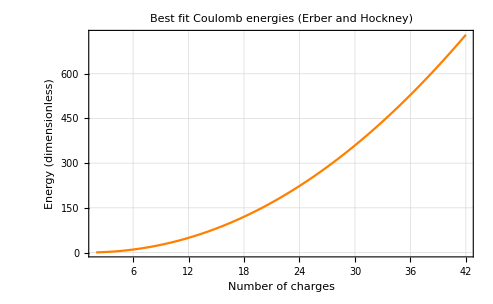

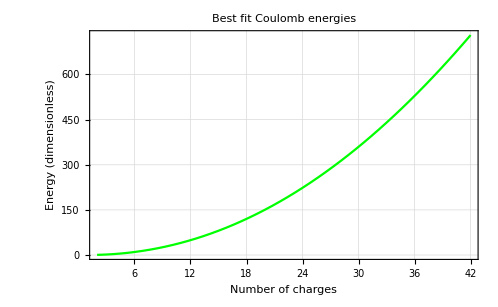

```mathematica
dot1=ListPlot[datapaper,Frame->True,FrameLabel->{"Number of charges","Energy (dimensionless)"},GridLines->Automatic,PlotLabel->"Coulomb energies for different numbers of charges (Erber and Hockney)",BaseStyle->{FontSize->11,FontFamily->"Helvetica"},PlotStyle->Orange]
dot2=ListPlot[dataprogram,Frame->True,FrameLabel->{"Number of charges","Energy (dimensionless)"},GridLines->Automatic,PlotLabel->"Coulomb energies for different numbers of charges",BaseStyle->{FontSize->11,FontFamily->"Helvetica"},PlotStyle->Green]
fitpaper[x_]:=Evaluate[Fit[datapaper,{1,x,x^2,x^3,x^4},x]]
fitprogram[x_]:=Evaluate[Fit[dataprogram,{1,x,x^2,x^3,x^4},x]]
plotpaper=Plot[fitpaper[x],{x,2,42},Frame->True,FrameLabel->{"Number of charges","Energy (dimensionless)"},GridLines->Automatic,PlotLabel->"Best fit Coulomb energies (Erber and Hockney)",BaseStyle->{FontSize->11,FontFamily->"Helvetica"},PlotStyle->Orange]
plotprogram=Plot[fitprogram[x],{x,2,42},Frame->True,FrameLabel->{"Number of charges","Energy (dimensionless)"},GridLines->Automatic,PlotLabel->"Best fit Coulomb energies",BaseStyle->{FontSize->11,FontFamily->"Helvetica"},PlotStyle->Green]
```

```mathematica
error=Table[{N[k],Abs[datapaper[[k,2]]-dataprogram[[k,2]]]},{k,2,33}]
```

{{2.,2.4×10^-9},{3.,0.},{4.,5.×10^-9},{5.,0.},{6.,2.1×10^-8},{7.,0.00010776},{8.,6.77×10^-6},{9.,0.00002794},{10.,0.00025722},{11.,4.×10^-8},{12.,0.00006007},{13.,0.0005209},{14.,0.00046972},{15.,0.0007301},{16.,0.00030886},{17.,0.00040335},{18.,0.00132523},{19.,0.00125899},{20.,0.0003529},{21.,0.00098195},{22.,0.00182954},{23.,0.00169185},{24.,0.0016058},{25.,0.00207688},{26.,0.00073887},{27.,0.00128844},{28.,0.00370008},{29.,0.0030618},{30.,0.00218984},{31.,5.×10^-8},{32.,0.00217705},{33.,0.00425362}}

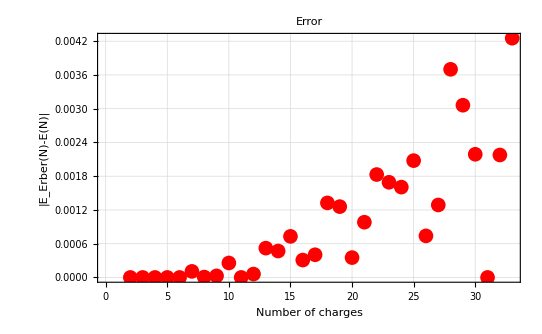

```mathematica
ploterror=ListPlot[error,Frame->True,FrameLabel->{"Number of charges","|\!\(\*SubscriptBox[\(E\), \(Erber\)]\)(N)-E(N)|"},GridLines->Automatic,PlotLabel->"Error",BaseStyle->{FontSize->11,FontFamily->"Helvetica"},PlotStyle->Red]
```